## 半人马座

```mathematica
M=1.99 10^30;AU=1.5 10^11;R1=6AU;R2=5.5 AU;R3=13000AU;m1=1.08M;m2=0.91M;m3=0.12M;
G=6.67 10^-11;ye=100*365 24 3600;alpha=2;
```

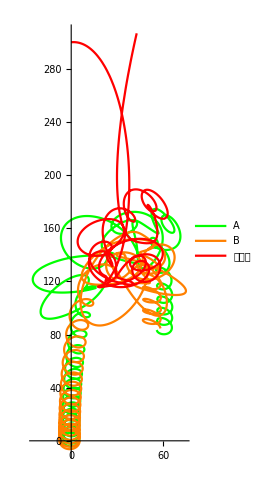

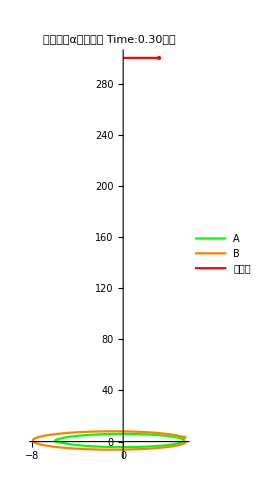
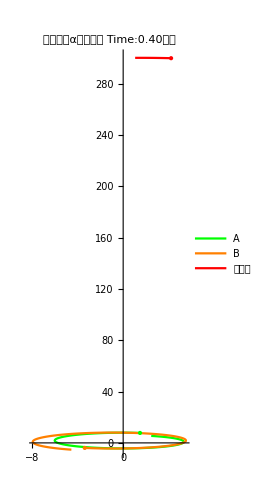
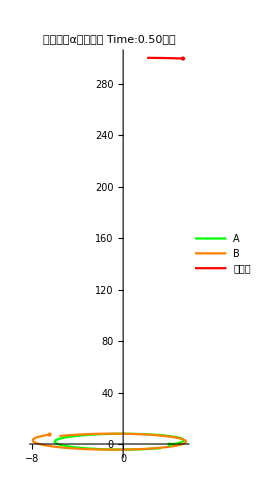
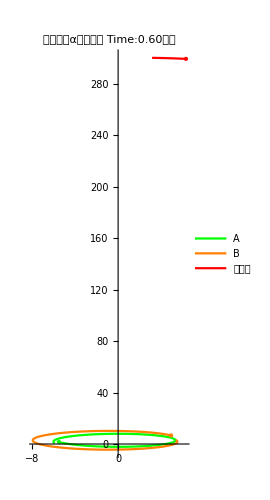
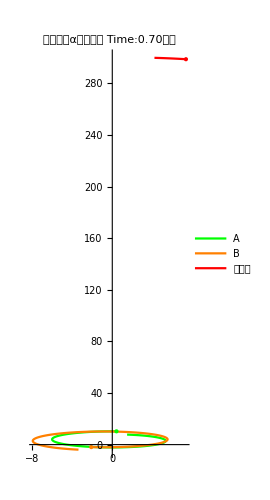
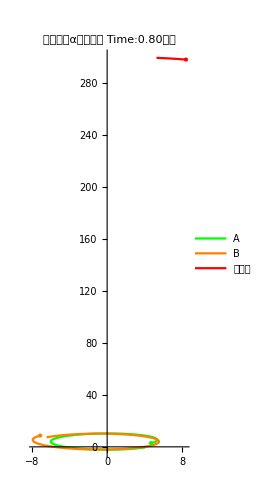
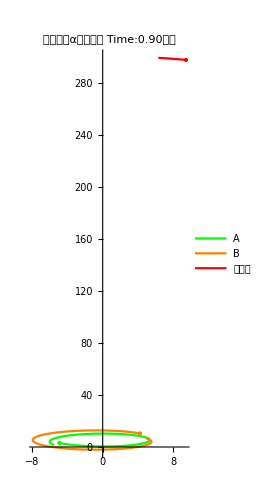
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

threebody.gif

```mathematica
Module[{x1,x2,x3,y1,y2,y3,tt},tt=15;so1=NDSolve[{x1''[t]==-G ((M (x1[t]-x3[t]))/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^((alpha+1)/2)+(m2 (x1[t]-x2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),y1''[t]==-G ((M (y1[t]-y3[t]))/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^((alpha+1)/2)+(m2 (y1[t]-y2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),x2''[t]==-G ((M (x2[t]-x3[t]))/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^((alpha+1)/2)+(m1 (x2[t]-x1[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),y2''[t]==-G ((M (y2[t]-y3[t]))/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^((alpha+1)/2)+(m1 (y2[t]-y1[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),
x3''[t]==-G ((m1 (x3[t]-x1[t]))/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2)^((alpha+1)/2)+(m2 (x3[t]-x2[t]))/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2)^((alpha+1)/2)),y3''[t]==-G ((m1 (y3[t]-y1[t]))/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2)^((alpha+1)/2)+(m2 (y3[t]-y2[t]))/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2)^((alpha+1)/2)),
x1[0]==-R1,x1'[0]==0,y1[0]==0,y1'[0]==6100,x2[0]==R2,x2'[0]==0,y2[0]==0,y2'[0]==-6700,x3[0]==0,x3'[0]==500,y3[0]==50R1,y3'[0]==60},{x1,y1,x2,y2,x3,y3},{t,0,tt ye}];
{x1,y1,x2,y2,x3,y3}={x1,y1,x2,y2,x3,y3}/.so1[[1]];
Print[ParametricPlot[{{x1[t],y1[t]}/AU,{x2[t],y2[t]}/AU,{x3[t],y3[t]}/AU},{t,0,tt ye },PlotStyle->{Green,Orange,Red},PlotLegends->{"A","B","比邻星"}]];
Print[Manipulate[Show[ParametricPlot[{{x1[τ]/AU,y1[τ]/AU},{x2[τ]/AU,y2[τ]/AU},{x3[τ]/AU,y3[τ]/AU}},{τ,(t-0.3) ye,t ye},PlotStyle->{Green,Orange,Red},PlotLegends->{"A","B","比邻星"},PlotLabel->"半人马座α三星系统\nTime:"<>ToString[NumberForm[t,{Infinity,2}]]<>"世纪"],Graphics[{Green,Point[{x1[t ye]/AU,y1[t ye]/AU}],Orange,Point[{x2[t ye]/AU,y2[t ye]/AU}],Red,PointSize[Large],Point[{x3[t ye]/AU,y3[t ye]/AU}]}]],{t,0.3,tt }]];
s=Table[Show[ParametricPlot[{{x1[τ]/AU,y1[τ]/AU},{x2[τ]/AU,y2[τ]/AU},{x3[τ]/AU,y3[τ]/AU}},{τ,(t-0.3) ye,t ye},PlotStyle->{Green,Orange,Red},PlotLegends->{"A","B","比邻星"},PlotLabel->"半人马座α三星系统\nTime:"<>ToString[NumberForm[t,{Infinity,2}]]<>"世纪"],Graphics[{Green,PointSize[Large],Point[{x1[t ye],y1[t ye]}/AU],Orange,PointSize[Large],Point[{x2[t ye],y2[t ye]}/AU],Red,PointSize[Large],Point[{x3[t ye],y3[t ye]}/AU]}]],{t,0.3,tt,0.1}];
Print[s];
Export["threebody.gif",s,"DisplayDurations"->0.06]]
```